```mathematica
na = Table[RandomInteger[{-1000,1000}],1000];
```

```mathematica
xa = Table[RandomInteger[{-1000,1000}],1000];
```

```mathematica
da = Table[RandomInteger[{-1000,1000}],1000];
```

```mathematica
exp = Table[RandomInteger[{-100,100}],1000];
```

```mathematica
na1 = Table[RandomInteger[{-1000,1000}],100];
```

```mathematica
xa1 = Table[RandomInteger[{-1000,1000}],100];
```

```mathematica
da1 = Table[RandomInteger[{-1000,1000}],100];
```

```mathematica
exp1 = Table[RandomInteger[{-100,100}],100];
```

```mathematica
maybe = Table[Binarize[Plot[ ((da[[xal]])*(x^2))+x*xa[[xal]]+exp[[xal]],{x,-10,10},Axes-> False,PlotRange->{-1000,1000}]]-> If[(da[[xal]])>0,"Ascending Parabola","Descending Parabola"],{xal,1,1000,1}];
```

```mathematica
association = maybe;
```

```mathematica
Part[association,1;;100]
```

{-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola}

```mathematica
association1 = Table[Binarize[Plot[ (da[[xal]]+(x))/(x)+na[[xal]],{x,-10,10},Axes-> False,PlotRange->{-1000,1000}]]-> "Hyperbolic",{xal,1,1000,1}];
```

```mathematica
TrainSet =Join[association,association1];
```

```mathematica
Part[TrainSet,1;;100]
```

```mathematica
association1test = Table[Binarize[Plot[ (da1[[xal]]+(x))/(x)+na1[[xal]],{x,-10,10},Axes-> False,PlotRange->{-1000,1000}]]-> "Hyperbolic",{xal,1,100,1}];
```

```mathematica
associationtest = Table[Binarize[Plot[ ((da1[[xal]])*(x^2))+x*xa1[[xal]]+exp1[[xal]],{x,-10,10},Axes-> False,PlotRange->{-1000,1000}]]-> If[(da1[[xal]])>0,"Ascending Parabola","Descending Parabola"],{xal,1,100,1}];
```

```mathematica
TestSet =Join[associationtest,association1test];
```

```mathematica
tempNet=Take[NetModel["Inception V3 Trained on ImageNet Competition Data"],{1,-4}]
```

NetChain[<>]

```mathematica
newNet=NetChain[<|"pretrainedNet"->tempNet,"linearNew"->LinearLayer[],"softmax"->SoftmaxLayer[]|>,"Output"->NetDecoder[{"Class",{"Ascending Parabola","Hyperbolic","Descending Parabola"}}]]
```

NetChain[<>]

```mathematica
trainedNet=NetTrain[newNet,TrainSet,LearningRateMultipliers->{"linearNew"->1,_->0}]
```

NetChain[<>]

```mathematica
ClassifierMeasurements[trainedNet,TestSet,"Accuracy"]
```

0.915

```mathematica
dal = Classify[TrainSet]
```

```mathematica
TrainSet
```

{-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Descending Parabola,-Graphics-→Ascending Parabola,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic,-Graphics-→Hyperbolic}

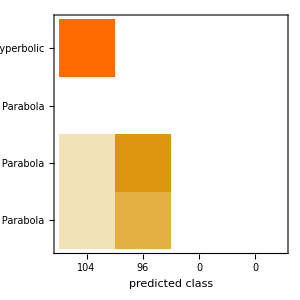

```mathematica
cm4=ClassifierMeasurements[dal,TestSet,"ConfusionMatrixPlot"]
```

```mathematica
cm1=ClassifierMeasurements[trainedNet1,TestSet,"Accuracy"]
```

0.955

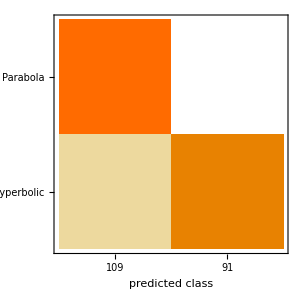

```mathematica
cm2=ClassifierMeasurements[trainedNet1,TestSet,"ConfusionMatrixPlot"]
```

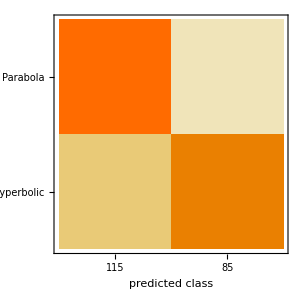

```mathematica
cm=ClassifierMeasurements[trainedNet,TestSet,"ConfusionMatrixPlot"]
```

```mathematica
cm["ConfusionMatrixPlot"]
```

1.[ConfusionMatrixPlot]

```mathematica
NetModel["ResNet-152 Trained on ImageNet Competition Data"]
```

NetChain[<>]

```mathematica
tempNet1=Take[NetModel["ResNet-152 Trained on ImageNet Competition Data"],{1,-4}]
```

NetChain[<>]

```mathematica
newNet1=NetChain[<|"pretrainedNet"->tempNet,"linearNew"->LinearLayer[],"softmax"->SoftmaxLayer[]|>,"Output"->NetDecoder[{"Class",{"Parabola","Hyperbolic"}}]]
```

NetChain[<>]

```mathematica
trainedNet1=NetTrain[newNet,TrainSet,LearningRateMultipliers->{"linearNew"->1,_->0}]
```

NetChain[<>]